```mathematica
Quit
```

4.8

NormalDistribution[0,4.8]

TemporalData[…]

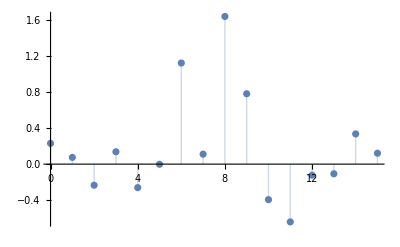

```mathematica
Tf=15;
umax = 4.8
NormalDistribution[0,umax]
data = RandomFunction[P,{0,15}]
ListPlot[data,Filling-> Axis]
```

4.8

NormalDistribution[0,4.8]

7.6591

InterpolatingFunction[{{0., 15.}}, <>][t]

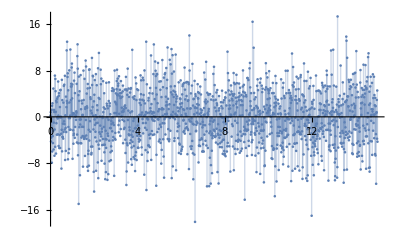

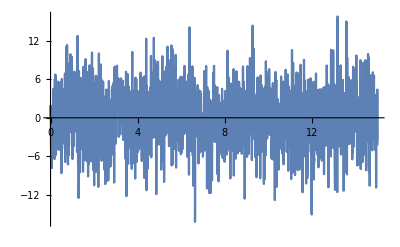

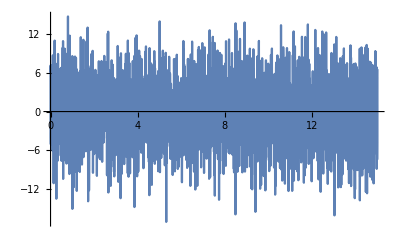

```mathematica
Tf=15;
umax = 4.8
P=NormalDistribution[0,umax]
RandomVariate[P]
data = Table[{t,RandomVariate[P]},{t,0,Tf,0.01}];
data2 =Interpolation[data][t]
ListPlot[data,Filling-> Axis]
Plot[data2,{t,0,Tf}]
urand[t_?NumericQ]:=RandomVariate[NormalDistribution[0,umax]];
Plot[urand[t],{t,0,Tf}]
```

```mathematica
SACcalc[U1_,tcurr_,InitCon_]:=Module[{to,tf,xsol,ρsol,J1init,ΔJmin,αd,Λ,u2,dJdλ,Jτm,Jτmlist,τmIndex,τm,k,ω,J1new,λ,u1temp,xsol2,U1R,tcurrR,InitConR},
{to,tf}={tcurr,tcurr+T}(*2*);
xsol =xtraj[InitCon,to,tf,U1](*3a*);
ρsol=ρsolve[xsol,to,tf](*3b*);
J1init =Cost[xsol,U1,to,tf](*4*);
ΔJmin =0(*-0.05*J1init*);
αd=γ*J1init(*5*);
Λ=hxᵀ.ρsol.ρsolᵀ.hx/.Thread[Flatten[X]-> Flatten[xsol]](*6a*);
u2=Inverse[Λ+Rᵀ].(Λ.U1+hxᵀ.ρsol*αd)/.Thread[Flatten[X]-> Flatten[xsol]](*6b*);
dJdλ = ρsolᵀ.(f[xsol,u2]-f[xsol,U1])(*7a*);
Jτm= Norm[u2]+dJdλ+(t-to)^β(*7b*);
Jτmlist=Table[Flatten[{t,Jτm}],{t,to,tf,0.01}];
(*Jτm=Interpolation[Jτmlist][t](*7c*);*)
τmIndex = Position[Jτmlist[[1;;,2]],Min[Jτmlist[[1;;,2]]]][[1,1]];
τm=(*Chop[GSSearch[Jτm,to,tf]]*)(*7final*)(*Chop[NMinimize[{Jτm,to≤ t≤ tf},t][[2,1,2]]]*)Jτmlist [[τmIndex,1]];
Subscript[u2, i]={{Saturation[(u2/.t-> Subscript[τm, i])[[1,1]],umax]}}(*8*);

k=0; ω=0.55;J1new = Infinity (*9*);

While[J1new-J1init>ΔJmin && k≤ kmax,
     λ=Δtinit*ω^k(*10a*);
     {τo,τf}=Chop[{Subscript[τm, i]-λ/2,Subscript[τm, i]+λ/2}](*10b*);
     {τo,τf}=uInterval[Interval[to,to+ts],Interval[τo,τf]];
     u1temp = Piecewise[{{Subscript[u2, i][[1,1]],τo≤ t≤ τf}},U1[[1,1]]];
      xsol2 = xtraj[InitCon,to,tf,{{u1temp}}](*10c*);
     J1new = Cost[xsol2,{{u1temp}},to,tf](*10d*);
     k++(*10e*);
](*end inner while*);


xsol2 = xtraj[InitCon,to,tf,{{u1temp}}](*10c*);
u1temp=PiecewiseExpand[u1temp];

U1R={{u1temp}};
tcurrR=tcurr+ts;
InitConR=Thread[Flatten[X/.t-> tcurr]==Flatten[xsol2/.t-> tcurr]];
]
```